## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

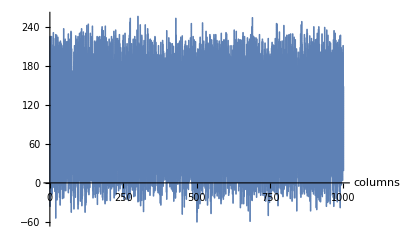

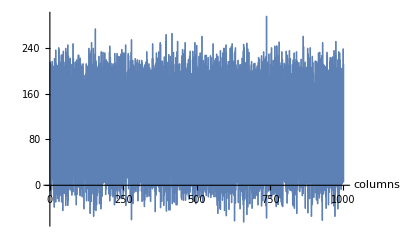

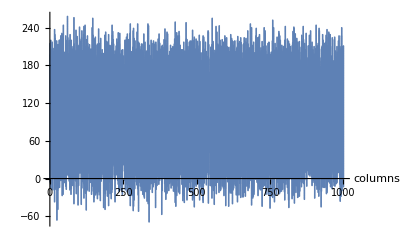

```mathematica
Do[top=ReadList[TemplateApply["C:\\Users\\刘兴瑞\\Documents\\Visual Studio 2015\\Projects\\pillars\\pillars\\top``.txt",{i}],Number];
bottom=ReadList[TemplateApply["C:\\Users\\刘兴瑞\\Documents\\Visual Studio 2015\\Projects\\pillars\\pillars\\bottom``.txt",{i}],Number];
pillar={};
Do[Do[pillar=Append[pillar,{i,top[[i]]-j+1}],{j,1,top[[i]]-bottom[[i]]-1}],{i,1,Length[top]}]
Print[ListPlot[pillar,AxesLabel->{"columns",""}]],{i,1,3}]
```

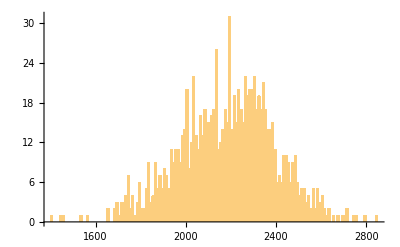

```mathematica
failTime=Flatten[Import["pillars/fail_time.csv"]];
Histogram[failTime,100]
```

```mathematica
|
```

```mathematica
|
```

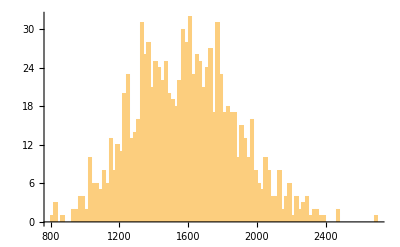

```mathematica
variance=ReadList["C:\\Users\\刘兴瑞\\Documents\\Visual Studio 2015\\Projects\\pillars\\pillars\\variance.csv",Number];
Histogram[variance,100]
```

```mathematica
varianceFile="C:\\Users\\刘兴瑞\\Documents\\Visual Studio 2015\\Projects\\pillars\\pillars\\variance.csv";
```

C:\Users\刘兴瑞\Documents\Visual Studio 2015\Projects\pillars

```mathematica
variance=Import["pillars/variance.csv"];
```